```mathematica
(*Final*)
```

```mathematica
(* -------------- Matrix functions ---------------*)

Rotz4[θ_]:=({{Cos[θ], -Sin[θ], 0, 0}, {Sin[θ], Cos[θ], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})
Rotz[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}})
Vec3[v1_,v2_,v3_]:={{v1},{v2},{v3}}
Trans4[x_,y_]:=({{1, 0, 0, x}, {0, 1, 0, y}, {0, 0, 1, 0}, {0, 0, 0, 1}})
NewT4[x_,y_,θ_]:=Trans4[x,y].Rotz4[θ]
Zeros[dim1_,dim2_]:=Table[0,{i,1,dim1},{j,1,dim2}]
MF[T_]:=MatrixForm[T]

(* Geometrical transformation funcs *)
Hat[ω_]:=({{0, -ω[[3,1]], ω[[2,1]]}, {ω[[3,1]], 0, -ω[[1,1]]}, {-ω[[2,1]], ω[[1,1]], 0}})
Unhat[ω_]:={{ω[[3,2]]},{ω[[1,3]]},{ω[[2,1]]}}

(* generalized hat: g -> twist *)
Genhat2[ω_,v_]:=ArrayFlatten[({{Hat[ω], v}, {Zeros[1,3], 0}})]
Genhat[S_]:=Module[{ω,v},
ω=S[[1;;3,1;;1]];
v=S[[4;;6,1;;1]];
Genhat2[ω,v]
]
GenUnhat[T_]:=Join[Unhat[T[[1;;3,1;;3]]],T[[1;;3,4;;4]]]
AdT[T_]:=Module[{R,p},
R=T[[1;;3,1;;3]];
p=T[[1;;3,4;;4]];
ArrayFlatten[({{R, Zeros[3,3]}, {Hat[p].R, R}})]
]
InvT[T_]:=Module[{R,p},
R=T[[1;;3,1;;3]];
p=T[[1;;3,4;;4]];
ArrayFlatten[({{Transpose[R], -Transpose[R].p}, {Zeros[1,3], 1}})]
]
(*-------------- Funcs end. Below are the main program. --------------*)
```

```mathematica
(* ---------------- vars ----------------*)
nVars=0;
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
qs={};
qsvars={};
qsInit={};
dqsInit={};
(* ------------ objects ----------------- *)
nObjects=0;
objNames={};
(* Properties *)
l=l1=l2=l3=1;
w=w1=w2=w3=0.25;
masses={};
inertias={};
lens={l1,l2,l3};
widths={w1,w2,w3};
g=9.8;
(* Transformation matrices *)
Ts={};
```

```mathematica
(* ------------ Create objects ----------------- *)
CreateOneLink[{p1x_,p1y_},{p2x_,p2y_}]:=Module[{l,T1},
l=CalcDist[p1x,p1y,p2x,p2y];
mass=lToMass[l];
inertia=lToInertia[l];
(*Vars*)
nDOF=3;
{objqs,objqsvars}=newVars[nDOF];
x=objqsvars[[1]];
y=objqsvars[[2]];
θ=objqsvars[[3]];
(*Geometry*)
Tw=Trans4[0,0];
T1=Tw.Trans4[x[t],y[t]].Rotz4[θ[t]]//Simplify;
pFront=T1.Transpose[{{l/2,0,0,1}}]//Simplify;
pBack=T1.Transpose[{{-l/2,0,0,1}}]//Simplify;
(*Output/Update*)
nObjects=nObjects+1;
Ts=Append[Ts,T1];
masses=Append[masses,mass];
inertias=Append[inertias,inertia];
(* Init pose *)
objqsinit={(p1x+p2x)/2,(p1y+p2y)/2,myArcTan[p1x,p1y,p2x,p2y]};
qsInit=Join[qsInit,objqsinit];
dqsInit=Join[dqsInit,ConstantArray[0,nDOF]];
(*Return*)
T1
]

g1=CreateOneLink[{-0.5,-0.5},{0.5,0.5}];
MF[g1]
```

(Cos[$q3[t]] | -Sin[$q3[t]] | 0 | $q1[t]
Sin[$q3[t]] | Cos[$q3[t]] | 0 | $q2[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(* Prepare *)
dqs=D[qs,t];
ddqs=D[dqs,t];
qsInit=ConstantArray[0,nVars];
dqsInit=ConstantArray[0,nVars];
```

```mathematica
(* --------------- Left side of EL eqs -------------- *)
(* Body generalized mass, composed of Inertia Tensor and Mass Matrix *)
getGb[j_,m_]:=ArrayFlatten[({{DiagonalMatrix[{j,j,j}], Zeros[3,3]}, {Zeros[3,3], DiagonalMatrix[{m,m,m}]}})]
Gbs=Table[getGb[inertias[[i]],masses[[i]]],{i,1,nObjects}]//Simplify;
(* Body screw axis *)
Vbs=Table[GenUnhat[InvT[Ts[[i]]].D[Ts[[i]],t]],{i,1,nObjects}]//Simplify;
(* Lagrange Equations: Kinetic and Potential Energy *)
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
KEs=Table[GetKE[Gbs[[i]],Vbs[[i]]],{i,1,nObjects}]//Simplify;
PEs=Table[GetPE[masses[[i]],Ts[[i]]],{i,1,nObjects}]//Simplify;
Lag=Total[Join[KEs,-PEs]]//Simplify;
(* Left side of Euler-Lagrange Equations*)
ELeqsLeft=D[D[Lag,{dqs}],t]-D[Lag,{qs}]//Simplify;
```

```mathematica
(* --------------- Right side of EL eqs -------------- *)
(* Constraints *)
(*
conslink1P1x=p1Ends[[1]][[2,1]];(* y=0 *)
conslink1P1y=p1Ends[[2]][[2,1]];(* y=0 *)
*)
cons={}//Simplify;
nCons=Length[cons];
If[nCons>0,
(λs=Transpose[{Table[Symbol["$λ"<>ToString@i],{i,nCons}]}];
consgrad=Transpose[Grad[cons,qs]]; (* Grad[2,5]->Mat(2,5),Transpose->(5,2)*)
consddt=D[D[cons,t],t]//Simplify)];
```

```mathematica
(* External forces *)
externalForces=ConstantArray[0,nVars];
```

```mathematica
(* ----------------------------- *)
(* Solve *)
If[nCons>0,(* with constraints *)
(EulerLagEqs=Thread[ELeqsLeft==Flatten[consgrad.λs]+externalForces]//Simplify;
consddtEqs=TurnToEq[consddt,ConstantArray[0,nCons]];
EQ=Solve[Join[EulerLagEqs,consddtEqs],Join[ddqs,Flatten[λs]]]),
(* No constraint *)
EulerLagEqs=TurnToEq[ELeqsLeft,externalForces]//Simplify;
EQ=Solve[EulerLagEqs,ddqs]];
```

```mathematica
(* Preprae for NDSolve *)
SetUpImpacts[]
ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];

(* NDsolve *)
timeend=2;
MAXIMPACTTIMES=3;

ifprint=True;
impactDetectionError=0.01;
intergrationMaxStepSize=0.01;

{end,data,bounces}=BouncingBall[qsInit,dqsInit];
```

Impact detected at: t=0.638877,impactcase=0

Before reflection, q={0.,-2.,0.},dq={0.,-6.26099,0.}

After reflection{0.,6.26099,0.}

Impact detected at: t=1.91663,impactcase=0

Before reflection, q={0.,-2.,0.},dq={0.,-6.26099,0.}

After reflection{0.,6.26099,0.}

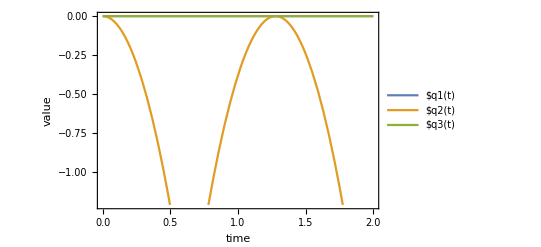

```mathematica
(* Plot *)
qsPlot=Table[Piecewise[qsvars[[i]]/.data],{i,1,nVars}];
Show[Plot[Evaluate[qsPlot],{t,0,end},PlotLegends->qs,
	PlotRange->Automatic,Frame->True,FrameLabel->{"time","value"}]]
```

```mathematica
plotGetLinkCoords[T_,l_]:=Module[{pFront,pBack},
p0x=T[[1,4]];
p0y=T[[2,4]];
pFront=T.Transpose[{{l/2,0,0,1}}]//Simplify;
pBack=T.Transpose[{{-l/2,0,0,1}}]//Simplify;
Line[{pFront[[1;;2,1]],pBack[[1;;2,1]]}]
]
links=Table[plotGetLinkCoords[Ts[[i]],lens[[i]]],{i,1,nObjects}];
```

```mathematica
(* Animate *)
(*linksCoords[i_]:=(links[[i]]/.sim)[[1]];*)
linksCoords[j_]:=links[[j]]/.Table[qs[[i]]->qsPlot[[i]],{i,1,nVars}];
LinksForAnimation[tt_]:=(Table[linksCoords[i],{i,1,Length[links]}])/.t->tt;
Animate[Show[
{Graphics[LinksForAnimation[t][[1]]]
},PlotRange-> {{-3,3},{-30,3}},Frame-> True],{t,0,timeend}]
```